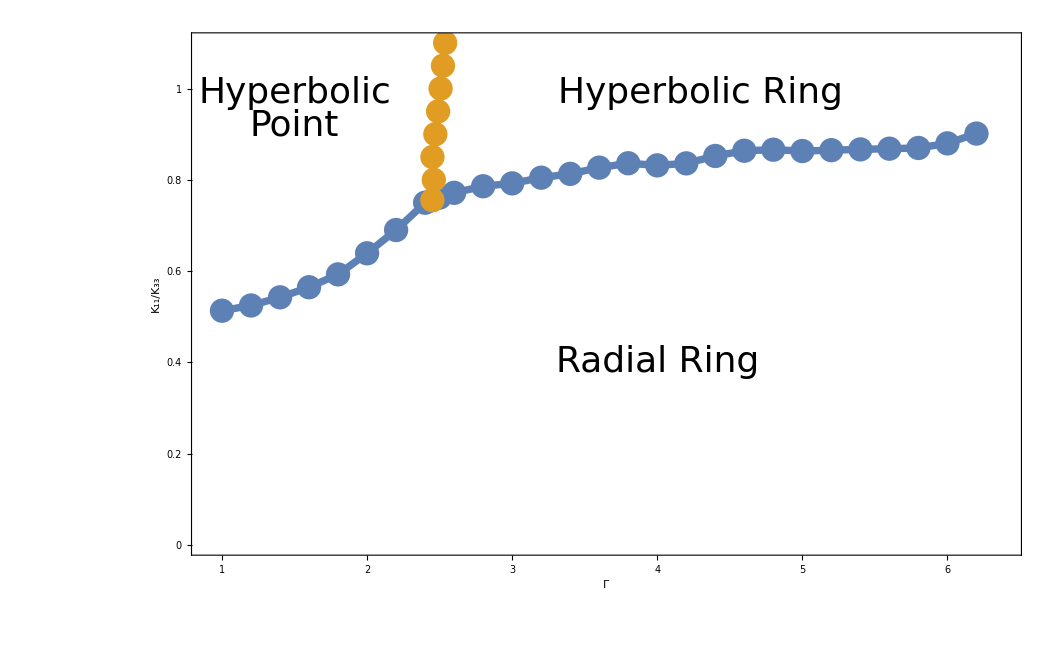

```mathematica
aa={{1,0.51345},{1.2,0.524834},{1.4,0.54271},{1.6,0.564809},{1.8,0.592971},{2,0.639201},{2.2,0.69013},{2.4,0.749939},{2.45, (0.761315+0.749939)/2},{2.5,0.761315},{2.6,0.771614},{2.8,0.786021},{3,0.792309},{3.2,0.804773},{3.4,0.81311},{3.6,0.826744},{3.8,0.836397},{4,0.831741},
{4.2, 0.836135},{4.4,0.852303},{4.6,0.863789},{4.8,0.866068},{5,0.863156},{5.2,0.865022},{5.4,0.866725},{5.6,0.868319},
{5.8,0.869846},{6,0.879924},{6.2,0.901416}
};
bb={{2.45, (0.761315+0.749939)/2},{2.45986,0.8},{2.45048,0.85},{2.47049,0.9},{2.48962,0.95},{2.50661,1},{2.52297,1.05},{2.53818,1.1}};
ListPlot[{aa,bb},PlotStyle->{Thickness[0.005]},Joined->{True, True},PlotMarkers->{Graphics[{Disk[]},ImageSize->25],Graphics[{Disk[]},ImageSize->25]}, PlotRange->{{0.9,6.4},Automatic}, Frame->{True, True, False, False}, FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},None},{{1,2,3,4,5,6},None}},FrameTicksStyle->Directive[Black,36],LabelStyle->Directive[Black,36],FrameLabel->{{"K_11/K_33", None},{"Γ", None}},FrameStyle->Thickness[0.005],Epilog->{Text[Style["Hyperbolic",Directive[Black,36]],{1.5,0.99}],Text[Style["Point",Directive[Black,36]],{1.5,0.92}],Text[Style["Hyperbolic Ring",Directive[Black,36]],{4.3,0.99}],Text[Style["Radial Ring",Directive[Black,36]],{4.0,0.4}]}]
```